# Example 4A - Test on the cv of the N distribution

Data

```mathematica
xmean=17;
ssquare=1.6;
n=10 ;
m=40;
psiH=0.1;
```

Hyperparameters

```mathematica
eta1=xmean;
nu1=n;
alpha1=n/2;
beta1=(n*ssquare)/2;
```

Normalizing constant

```mathematica
c1 = NIntegrate[(Sqrt[(nu1*y)/(2*Pi)]*Exp[(-0.5*nu1*y)*((x-eta1)^2)]*((beta1^alpha1)/Gamma[alpha1])*((y)^(alpha1-1))*Exp[-beta1*y]),{x,10,30},{y,0.01,5}];
```

Normalized Posterior distribution

```mathematica
gposterior1=(1/c1)*(Sqrt[(nu1*y)/(2*Pi)]*Exp[(-0.5*nu1*y)*((x-eta1)^2)]*((beta1^alpha1)/Gamma[alpha1])*((y)^(alpha1-1))*Exp[-beta1*y]);
```

```mathematica
NIntegrate[gposterior1,{x,10,30},{y,0.01,5}]
```

1.

## Flat reference function [A]

```mathematica
yr=1/(psiH*x)^2;
```

```mathematica
gprofile1=(1/c1)*(Sqrt[(nu1*yr)/(2*Pi)]*Exp[(-0.5*nu1*yr)*((x-eta1)^2)]*((beta1^alpha1)/Gamma[alpha1])*((yr)^(alpha1-1))*Exp[-beta1*yr]);
```

```mathematica
FindMaximum[gprofile1,{x,15}]
```

{0.917243,{x→16.9422}}

Level

```mathematica
kFlatA= 0.9172425464466639
```

0.917243

Region

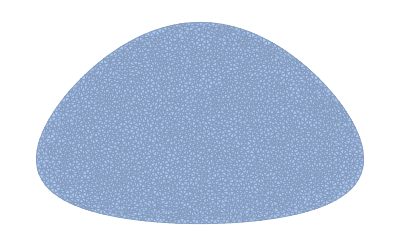

```mathematica
TbarFlatA=DiscretizeRegion[ImplicitRegion[gposterior1>kFlatA,{x,y}],{{13,21},{0.01,2.5}},MaxCellMeasure->0.0001]
```

```mathematica
RegionPlot[TbarFlatA]
```

-Graphics-

```mathematica
TbarFlatAComplementary=DiscretizeRegion[ImplicitRegion[gposterior1<=kFlatA,{x,y}],{{16,18},{0.01,1}},MaxCellMeasure->0.0001]
```

-Graphics-

Integral

```mathematica
g1A[x,y]:=(1/c1)*(Sqrt[(nu1*y)/(2*Pi)]*Exp[(-0.5*nu1*y)*((x-eta1)^2)]*((beta1^alpha1)/Gamma[alpha1])*((y)^(alpha1-1))*Exp[-beta1*y]);
```

```mathematica
Integrate[g1A[x,y],{x,y}∈TbarFlatA]
```

0.364135

## Jeffreys prior as reference function [A]

Reference function

```mathematica
r=(y)^(-1);
```

Surprise function

```mathematica
s1=gposterior1/r;
```

```mathematica
yr=1/(psiH*x)^2;
```

Profile function

```mathematica
sprofile1=((1/c1)*(Sqrt[(nu1*yr)/(2*Pi)]*Exp[(-0.5*nu1*yr)*((x-eta1)^2)]*((beta1^alpha1)/Gamma[alpha1])*((yr)^(alpha1-1))*Exp[-beta1*(1/yr)]))/((yr)^(-1));
```

```mathematica
FindMaximum[sprofile1,{x,16}]
```

{1.92346×10^-9,{x→16.1847}}

Level

```mathematica
sstarA=1.92346483091942*^-9
```

1.92346×10^-9

Region

```mathematica
TbarJeffA=DiscretizeRegion[ImplicitRegion[s1>sstarA,{x,y}],{{13,21},{0.01,2.5}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarJeffA]
```

-Graphics-

```mathematica
TbarJeffAComplementary=DiscretizeRegion[ImplicitRegion[s1<=sstarA,{x,y}],{{13,21},{0.01,2.5}},MaxCellMeasure->0.0001]
```

-Graphics-

Integral

```mathematica
Integrate[g1A[x,y],{x,y}∈TbarJeffA]
```

0.999998

# Example 4B - Test on the cv of the N distribution

Hyperparameters

```mathematica
eta2=xmean;
nu2=m;
alpha2=m/2;
beta2=(m*ssquare)/2;
```

Normalizing constant

```mathematica
c2 = NIntegrate[(Sqrt[(nu2*y)/(2*Pi)]*Exp[(-0.5*nu2*y)*((x-eta2)^2)]*((beta2^alpha2)/Gamma[alpha2])*((y)^(alpha2-1))*Exp[-beta2*y]),{x,15,20},{y,0.01,3}]
```

0.999998

Normalized Posterior distribution

```mathematica
gposterior2=(1/c2)*(Sqrt[(nu2*y)/(2*Pi)]*Exp[(-0.5*nu2*y)*((x-eta2)^2)]*((beta2^alpha2)/Gamma[alpha2])*((y)^(alpha2-1))*Exp[-beta2*y]);
```

```mathematica
NIntegrate[gposterior2,{x,15,20},{y,0.01,3}]
```

1.

## Flat reference function [B]

```mathematica
yr=1/(psiH*x)^2;
```

```mathematica
gprofile2=(1/c2)*(Sqrt[(nu2*yr)/(2*Pi)]*Exp[(-0.5*nu2*yr)*((x-eta2)^2)]*((beta2^alpha2)/Gamma[alpha2])*((yr)^(alpha2-1))*Exp[-beta2*yr]);
```

```mathematica
FindMaximum[gprofile2,{x,16}]
```

{0.435242,{x→16.9297}}

Level

```mathematica
kFlatB=0.4352419055493096
```

0.435242

Region

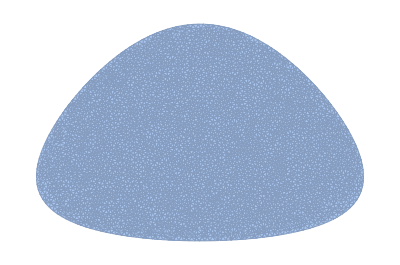

```mathematica
TbarFlatB=DiscretizeRegion[ImplicitRegion[gposterior2>kFlatB,{x,y}],{{16,18},{0.01,1.5}},MaxCellMeasure->0.0001]
```

```mathematica
RegionPlot[TbarFlatB]
```

-Graphics-

```mathematica
TbarFlatBComplementary=DiscretizeRegion[ImplicitRegion[gposterior2<=kFlatB,{x,y}],{{16,18},{0.01,1.5}},MaxCellMeasure->0.0001]
```

-Graphics-

Integral

```mathematica
g1B[x,y]:=(1/c2)*(Sqrt[(nu2*y)/(2*Pi)]*Exp[(-0.5*nu2*y)*((x-eta2)^2)]*((beta2^alpha2)/Gamma[alpha2])*((y)^(alpha2-1))*Exp[-beta2*y]);
```

```mathematica
Integrate[g1B[x,y],{x,y}∈TbarFlatB]
```

0.924094

## Jeffreys prior as reference function [B]

Reference function

```mathematica
r=(y)^(-1);
```

Surprise function

```mathematica
s2=gposterior2/r;
```

```mathematica
yr=1/(psiH*x)^2;
```

Profile function

```mathematica
sprofile2=((1/c2)*(Sqrt[(nu2*yr)/(2*Pi)]*Exp[(-0.5*nu2*yr)*((x-eta2)^2)]*((beta2^alpha2)/Gamma[alpha2])*((yr)^(alpha2-1))*Exp[-beta2*(1/yr)]))/((yr)^(-1));
```

```mathematica
Maximize[sprofile2,x]
```

{0.,{x→-6.96782}}

Level

```mathematica
sstarB=0.0000000001
```

1.×10^-10

Region

```mathematica
TbarJeffB=DiscretizeRegion[ImplicitRegion[s2>sstarB,{x,y}],{{13,21},{0.01,2.5}},MaxCellMeasure->0.0001]
```

-Graphics-

```mathematica
RegionPlot[TbarJeffB]
```

```mathematica
TbarJeffBComplementary=DiscretizeRegion[ImplicitRegion[s2<=sstarB,{x,y}],{{13,21},{0.01,2.5}},MaxCellMeasure->0.0001]
```

-Graphics-

Integral

```mathematica
Integrate[g1B[x,y],{x,y}∈TbarJeffB]
```

1.